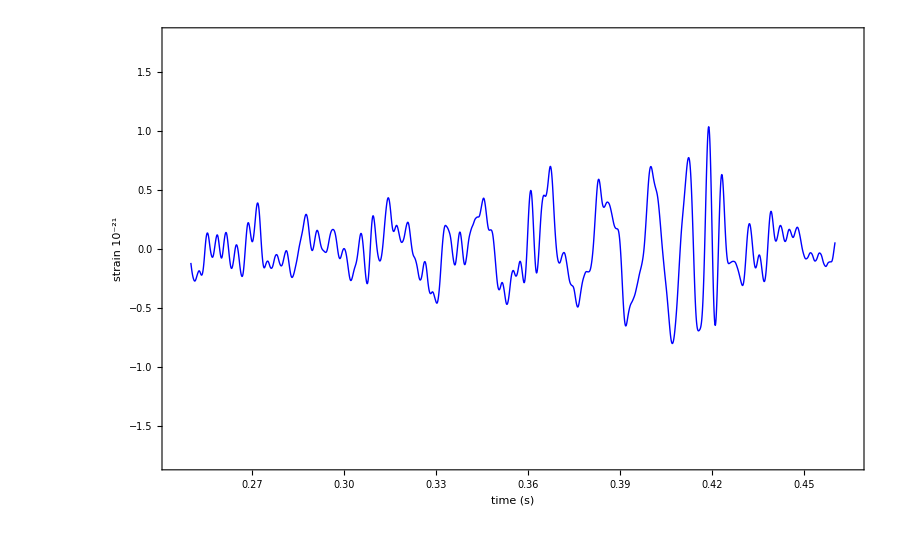

```mathematica
H1=ListPlot[Import["D:\\GW150914.txt","Table"],ImageSize->900,Frame->True,Joined->True,PlotRange->{{0.245,0.465},{-1.8,1.8}},BaseStyle ->{FontFamily->"Arial",18},FrameLabel->{"time (s)",(Subsuperscript["10","","-21"] )" strain " },PlotStyle->{Blue,Thickness[Medium]}]
```

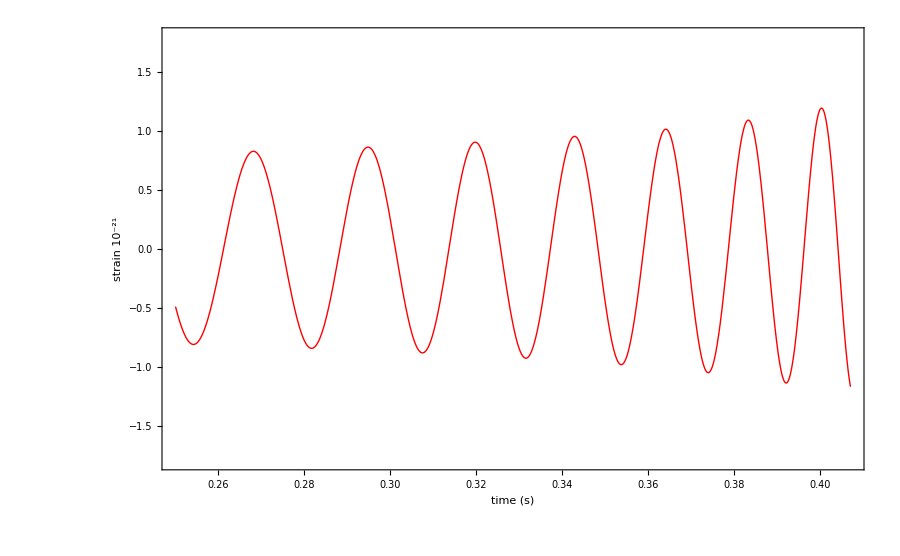

```mathematica
ClearAll[f0,m1,m2,mchirp,M,r,d];
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
M=mchirp[m1,m2]*4.92549095*10^(-6);
d=r*1.0292712503*10^8;
tmerg[M_,f0_]=5(256(N[π]f0)^(8/3)M^(5/3))^(-1);
F[M_,f0_,t_]=(M (f0)^9)^(1/8)((M f0)^(1/3)-256f0^3 M^2N[π]^(8/3)((t-0.25)/5))^(-3/8);Angle[M_,f0_,t_]=-2((256(N[π]M f0)^(8/3))^(-1)-((t-0.25)/(5M)))^(5/8);
Amplitude[M_,f0_,d_,t_]=4M^(5/3)N[π]^(2/3)(F[M,f0,t])^(2/3)d^(-1 );
m1=36;
m2=29;
f0=35;
r= 410*10^6;
H2=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0.25,0.4072},
PlotRange->{{0.25,0.4072},{-1.8,1.8}},PlotStyle->{Red,Thickness[Large]},Frame->True,ImageSize->900,BaseStyle ->{FontFamily->"Arial",18},FrameLabel->{"time (s)",(Subsuperscript["10","","-21"] )" strain " }]
```

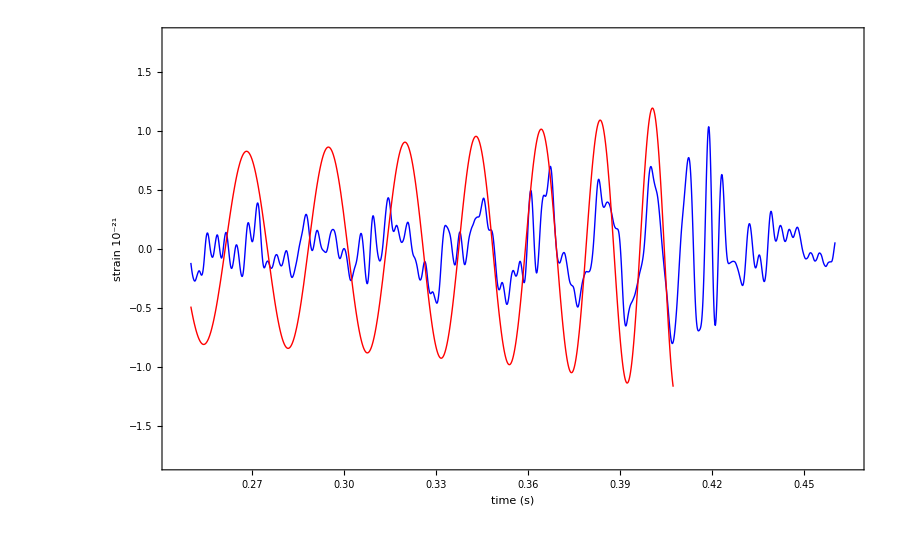

```mathematica
Needs["PlotLegends`"]
ShowLegend[Show[H1,H2],{{{Graphics[{Blue,Thickness[Large],Line[{{0,0},{1,0}}]}],Style["L1 Observed",Bold,15]},{Graphics[{Red,Thickness[Large],Line[{{0,0},{1,0}}]}],Style["Newtonian chirp",Bold,15]}},LegendSize->{0.52,0.3},LegendPosition->{1,0.3},LegendShadow->None}]
```